```mathematica
ClearAll["Global`*"]
Remove["Global`*"];
```

## Setting Cosmological History

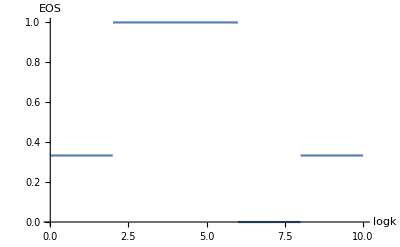

```mathematica
w=Piecewise[{{1,logk>2&&logk<6},{0,logk>6&&logk<8}},1/3];
beta=-2(1-3*w)/(1+3*w);
Plot[w,{logk,0,10},AxesLabel->{logk,EOS}]
```

## Gaussian input in Log scale

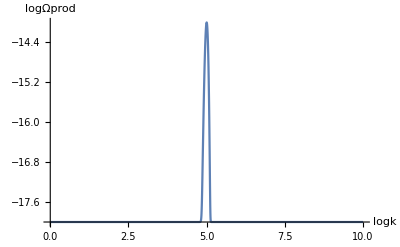

```mathematica
init=Log[10,(10^(-18)*(1+10000*Exp[-((10^x-100000)/10000)^2]))];
Plot[init,{x,0,10},AxesLabel->{logk,logΩprod}]
```

## Cosmological evolution Animation

```mathematica
Ω[x_,a_]:=init+UnitStep[x-(10-a)]*Integrate[beta,{logk,10-a,x},Assumptions->{x,a}∈Reals];
Animate[ParametricPlot[{{x,Ω[x,a]},{10-a,-10*x}},{x,0,10},AxesLabel->{logk,logΩ},PlotRange->{{0,10},{-24,-11}},ImageSize->{400,400},AspectRatio->Full],{a,0,10},AnimationRate->.4]
Animate[ ParametricPlot[{{logk,w},{10-a,10*logk-50}},{logk,0,10},AxesLabel->{logk,EOS},PlotRange->{{0,10},{-0.3,1.1}},ImageSize->{400,200},AspectRatio->Full],{a,0,10},AnimationRate->.4]
```